## SC/Coordinate generation

```mathematica
pos={0,0,-33960}(*km*);
dircen={0,0,1};
```

```mathematica
viewdir[θ_,ϕ_]=RotationMatrix[-θ,{1,0,0}].RotationMatrix[ϕ,{0,1,0}].dircen
```

{Sin[ϕ],Cos[ϕ] Sin[θ],Cos[θ] Cos[ϕ]}

```mathematica
Manipulate[Graphics3D[{Arrow[{{0,0,0},viewdir[θ,ϕ]}],{Yellow,Arrow[{{0,0,0},{1,0,0}}]}},PlotRange->{{-1,1},{-1,1},{0,1}}],{{θ,0},-π/2,π/2},{{ϕ,0},-π/2,π/2}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mike/Documents/Mars/3D_Thomas_model

```mathematica
θrange=Range[-30°,30°,1.°];
ϕrange=Range[-30°,30°,1.°];
```

```mathematica
Length[ϕrange]*Length[θrange]
```

3721

```mathematica
coordstable=Table[(Join[{1.0,0.1},pos,viewdir[θ,ϕ],{Norm[#],180/π ArcTan[#[[1]],√((#[[2]])^2+(#[[3]])^2)]/.Indeterminate->0}&@(pos-viewdir[θ,ϕ](viewdir[θ,ϕ].pos)),{10,10,0}]),{ϕ,ϕrange},{θ,{0}}]//Flatten[#,1]&;
```

ArcTan::indet: Indeterminate expression ArcTan[0., 0.] encountered.

```mathematica
DeleteCases[Position[coordstable,x_/;Not[NumericQ[x]],{2}],x_/;MemberQ[x,0]]
```

{}

```mathematica
coordstable=Join[{Range[Length[#]]-1},#ᵀ]ᵀ&@(DeleteCases[coordstable,x_/;x[[6;;7]]=={0.,0.}]//N);
coordsstring=Riffle[StringJoin[Join[{"  "},Riffle[ToString/@#,"  "]]]&/@(coordstable),"\n"]//StringJoin;
coordfile="   "<>ToString[Length[coordstable]]<>" 1.466 3.8976965e15 1.0460000e2 3376.242\n"<>coordsstring;Export["fake_corona_obs_small.dat",coordfile,"Text"];
```

```mathematica
coordfile
```

60 1.466 3.8976965e15 1.0460000e2 3376.242
  0  1.  0.1  0.  0.  -33960.  -0.5  0.  0.866025  16980.  150.  10.  10.  0.
  1  1.  0.1  0.  0.  -33960.  -0.48481  0.  0.87462  16464.1  151.  10.  10.  0.
  2  1.  0.1  0.  0.  -33960.  -0.469472  0.  0.882948  15943.3  152.  10.  10.  0.
  3  1.  0.1  0.  0.  -33960.  -0.45399  0.  0.891007  15417.5  153.  10.  10.  0.
  4  1.  0.1  0.  0.  -33960.  -0.438371  0.  0.898794  14887.1  154.  10.  10.  0.
  5  1.  0.1  0.  0.  -33960.  -0.422618  0.  0.906308  14352.1  155.  10.  10.  0.
  6  1.  0.1  0.  0.  -33960.  -0.406737  0.  0.913545  13812.8  156.  10.  10.  0.
  7  1.  0.1  0.  0.  -33960.  -0.390731  0.  0.920505  13269.2  157.  10.  10.  0.
  8  1.  0.1  0.  0.  -33960.  -0.374607  0.  0.927184  12721.6  158.  10.  10.  0.
  9  1.  0.1  0.  0.  -33960.  -0.358368  0.  0.93358  12170.2  159.  10.  10.  0.
  10  1.  0.1  0.  0.  -33960.  -0.34202  0.  0.939693  11615.  160.  10.  10.  0.
  11  1.  0.1  0.  0.  -33960.  -0.325568  0.  0.945519  11056.3  161.  10.  10.  0.
  12  1.  0.1  0.  0.  -33960.  -0.309017  0.  0.951057  10494.2  162.  10.  10.  0.
  13  1.  0.1  0.  0.  -33960.  -0.292372  0.  0.956305  9928.94  163.  10.  10.  0.
  14  1.  0.1  0.  0.  -33960.  -0.275637  0.  0.961262  9360.64  164.  10.  10.  0.
  15  1.  0.1  0.  0.  -33960.  -0.258819  0.  0.965926  8789.49  165.  10.  10.  0.
  16  1.  0.1  0.  0.  -33960.  -0.241922  0.  0.970296  8215.67  166.  10.  10.  0.
  17  1.  0.1  0.  0.  -33960.  -0.224951  0.  0.97437  7639.34  167.  10.  10.  0.
  18  1.  0.1  0.  0.  -33960.  -0.207912  0.  0.978148  7060.68  168.  10.  10.  0.
  19  1.  0.1  0.  0.  -33960.  -0.190809  0.  0.981627  6479.87  169.  10.  10.  0.
  20  1.  0.1  0.  0.  -33960.  -0.173648  0.  0.984808  5897.09  170.  10.  10.  0.
  21  1.  0.1  0.  0.  -33960.  -0.156434  0.  0.987688  5312.51  171.  10.  10.  0.
  22  1.  0.1  0.  0.  -33960.  -0.139173  0.  0.990268  4726.32  172.  10.  10.  0.
  23  1.  0.1  0.  0.  -33960.  -0.121869  0.  0.992546  4138.68  173.  10.  10.  0.
  24  1.  0.1  0.  0.  -33960.  -0.104528  0.  0.994522  3549.79  174.  10.  10.  0.
  25  1.  0.1  0.  0.  -33960.  -0.0871557  0.  0.996195  2959.81  175.  10.  10.  0.
  26  1.  0.1  0.  0.  -33960.  -0.0697565  0.  0.997564  2368.93  176.  10.  10.  0.
  27  1.  0.1  0.  0.  -33960.  -0.052336  0.  0.99863  1777.33  177.  10.  10.  0.
  28  1.  0.1  0.  0.  -33960.  -0.0348995  0.  0.999391  1185.19  178.  10.  10.  0.
  29  1.  0.1  0.  0.  -33960.  -0.0174524  0.  0.999848  592.684  179.  10.  10.  0.
  30  1.  0.1  0.  0.  -33960.  0.0174524  0.  0.999848  592.684  1.  10.  10.  0.
  31  1.  0.1  0.  0.  -33960.  0.0348995  0.  0.999391  1185.19  2.  10.  10.  0.
  32  1.  0.1  0.  0.  -33960.  0.052336  0.  0.99863  1777.33  3.  10.  10.  0.
  33  1.  0.1  0.  0.  -33960.  0.0697565  0.  0.997564  2368.93  4.  10.  10.  0.
  34  1.  0.1  0.  0.  -33960.  0.0871557  0.  0.996195  2959.81  5.  10.  10.  0.
  35  1.  0.1  0.  0.  -33960.  0.104528  0.  0.994522  3549.79  6.  10.  10.  0.
  36  1.  0.1  0.  0.  -33960.  0.121869  0.  0.992546  4138.68  7.  10.  10.  0.
  37  1.  0.1  0.  0.  -33960.  0.139173  0.  0.990268  4726.32  8.  10.  10.  0.
  38  1.  0.1  0.  0.  -33960.  0.156434  0.  0.987688  5312.51  9.  10.  10.  0.
  39  1.  0.1  0.  0.  -33960.  0.173648  0.  0.984808  5897.09  10.  10.  10.  0.
  40  1.  0.1  0.  0.  -33960.  0.190809  0.  0.981627  6479.87  11.  10.  10.  0.
  41  1.  0.1  0.  0.  -33960.  0.207912  0.  0.978148  7060.68  12.  10.  10.  0.
  42  1.  0.1  0.  0.  -33960.  0.224951  0.  0.97437  7639.34  13.  10.  10.  0.
  43  1.  0.1  0.  0.  -33960.  0.241922  0.  0.970296  8215.67  14.  10.  10.  0.
  44  1.  0.1  0.  0.  -33960.  0.258819  0.  0.965926  8789.49  15.  10.  10.  0.
  45  1.  0.1  0.  0.  -33960.  0.275637  0.  0.961262  9360.64  16.  10.  10.  0.
  46  1.  0.1  0.  0.  -33960.  0.292372  0.  0.956305  9928.94  17.  10.  10.  0.
  47  1.  0.1  0.  0.  -33960.  0.309017  0.  0.951057  10494.2  18.  10.  10.  0.
  48  1.  0.1  0.  0.  -33960.  0.325568  0.  0.945519  11056.3  19.  10.  10.  0.
  49  1.  0.1  0.  0.  -33960.  0.34202  0.  0.939693  11615.  20.  10.  10.  0.
  50  1.  0.1  0.  0.  -33960.  0.358368  0.  0.93358  12170.2  21.  10.  10.  0.
  51  1.  0.1  0.  0.  -33960.  0.374607  0.  0.927184  12721.6  22.  10.  10.  0.
  52  1.  0.1  0.  0.  -33960.  0.390731  0.  0.920505  13269.2  23.  10.  10.  0.
  53  1.  0.1  0.  0.  -33960.  0.406737  0.  0.913545  13812.8  24.  10.  10.  0.
  54  1.  0.1  0.  0.  -33960.  0.422618  0.  0.906308  14352.1  25.  10.  10.  0.
  55  1.  0.1  0.  0.  -33960.  0.438371  0.  0.898794  14887.1  26.  10.  10.  0.
  56  1.  0.1  0.  0.  -33960.  0.45399  0.  0.891007  15417.5  27.  10.  10.  0.
  57  1.  0.1  0.  0.  -33960.  0.469472  0.  0.882948  15943.3  28.  10.  10.  0.
  58  1.  0.1  0.  0.  -33960.  0.48481  0.  0.87462  16464.1  29.  10.  10.  0.
  59  1.  0.1  0.  0.  -33960.  0.5  0.  0.866025  16980.  30.  10.  10.  0.

## nH/T grid interpolation

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mike/Documents/Mars/3D_Thomas_model

```mathematica
nHgridpts=Exp[Range[Log[10000],Log[1000000],(Log[1000000]-Log[10000])/(100.-1)]]
```

{10000.,10476.2,10975.,11497.6,12045.,12618.6,13219.4,13848.9,14508.3,15199.1,15922.8,16681.,17475.3,18307.4,19179.1,20092.3,21049.,22051.3,23101.3,24201.3,25353.6,26560.9,27825.6,29150.5,30538.6,31992.7,33516.,35111.9,36783.8,38535.3,40370.2,42292.4,44306.2,46415.9,48626.,50941.4,53367.,55908.1,58570.2,61359.1,64280.7,67341.5,70548.,73907.2,77426.4,81113.1,84975.3,89021.5,93260.3,97701.,102353.,107227.,112332.,117681.,123285.,129155.,135305.,141747.,148497.,155568.,162975.,170735.,178865.,187382.,196304.,205651.,215443.,225702.,236449.,247708.,259502.,271859.,284804.,298365.,312572.,327455.,343047.,359381.,376494.,394421.,413201.,432876.,453488.,475081.,497702.,521401.,546228.,572237.,599484.,628029.,657933.,689261.,722081.,756463.,792483.,830218.,869749.,911163.,954548.,1.×10^6}

```mathematica
Tgridpts=Range[100,2000,10]
Tgridpts//Length
```

{100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500,510,520,530,540,550,560,570,580,590,600,610,620,630,640,650,660,670,680,690,700,710,720,730,740,750,760,770,780,790,800,810,820,830,840,850,860,870,880,890,900,910,920,930,940,950,960,970,980,990,1000,1010,1020,1030,1040,1050,1060,1070,1080,1090,1100,1110,1120,1130,1140,1150,1160,1170,1180,1190,1200,1210,1220,1230,1240,1250,1260,1270,1280,1290,1300,1310,1320,1330,1340,1350,1360,1370,1380,1390,1400,1410,1420,1430,1440,1450,1460,1470,1480,1490,1500,1510,1520,1530,1540,1550,1560,1570,1580,1590,1600,1610,1620,1630,1640,1650,1660,1670,1680,1690,1700,1710,1720,1730,1740,1750,1760,1770,1780,1790,1800,1810,1820,1830,1840,1850,1860,1870,1880,1890,1900,1910,1920,1930,1940,1950,1960,1970,1980,1990,2000}

191

```mathematica
allnHTpairs=Flatten[Outer[List,MovingAverage[nHgridpts,2],MovingAverage[Tgridpts,2]],1];
```

```mathematica
allnHTpairs
```

{{10238.1,105},{10238.1,115},{10238.1,125},{10238.1,135},{10238.1,145},{10238.1,155},{10238.1,165},{10238.1,175},{10238.1,185},{10238.1,195},18791,{977274.,1915},{977274.,1925},{977274.,1935},{977274.,1945},{977274.,1955},{977274.,1965},{977274.,1975},{977274.,1985},{977274.,1995}}
 |  |  |  |

```mathematica
allnHTpairs//Length
```

18810

```mathematica
nHTpairs=Union[Join[
Flatten[Outer[List,Sequence@@#]&@(MovingAverage[#,2]&/@{Select[nHgridpts,10000<#<50000&],Select[Tgridpts,100<#<2000&]}),1],
Flatten[Outer[List,Sequence@@#]&@(MovingAverage[#,2]&/@{Select[nHgridpts,10000<#<1000000&],Select[Tgridpts,100<#<600&]}),1]
]]
```

{{10725.6,115},{10725.6,125},{10725.6,135},{10725.6,145},{10725.6,155},{10725.6,165},{10725.6,175},{10725.6,185},{10725.6,195},{10725.6,205},9257,{932856.,505},{932856.,515},{932856.,525},{932856.,535},{932856.,545},{932856.,555},{932856.,565},{932856.,575},{932856.,585}}
 |  |  |  |

```mathematica
nHTpairs//Length
```

9276

```mathematica
allnHTpairs//Length
```

18810

```mathematica
?Complement
```

RowBox[{"Complement", "[", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["all", "TI"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] gives the elements in SubscriptBox[StyleBox["e", "TI"], StyleBox["all", "TI"]] that are not in any of the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]].

```mathematica
simstrings="./simulate_coronal_scan.x -n "<>ToString[#[[1]]]<>" -T "<>ToString[#[[2]]]<>" fake_corona_obs_small.dat"&/@nHTpairs;
```

```mathematica
?RandomSample
```

RowBox[{"RandomSample", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["n", "TI"]}], "]"}] gives a pseudorandom sample of StyleBox["n", "TI"] of the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]].
RowBox[{"RandomSample", "[", RowBox[{RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["w", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "→", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], ",", StyleBox["n", "TI"]}], "]"}] gives a pseudorandom sample of StyleBox["n", "TI"] of the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]] chosen using weights SubscriptBox[StyleBox["w", "TI"], StyleBox["i", "TI"]].
RowBox[{"RandomSample", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] gives a pseudorandom permutation of the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]].

```mathematica
simfiletext=StringJoin[Riffle[RandomSample[simstrings],"\n"]];
```

```mathematica
Export["populate_parameter_space_commands",simfiletext,"Text"]
```

populate_parameter_space_commands

```mathematica
nHTpairs//Length
```

9276

```mathematica
remainingnHTpairs=Complement[allnHTpairs,nHTpairs];
remainingnHTpairs//Length
```

9534

```mathematica
9534*2
```

19068

```mathematica
remainingsimstrings="sleep 2; cd /lustre/janus_scratch/chaffin/3d_thomas_model/; ./simulate_coronal_scan.x -n "<>ToString[#[[1]]]<>" -T "<>ToString[#[[2]]]<>" fake_corona_obs_small.dat"&/@remainingnHTpairs;
```

```mathematica
remainingsimfiletext=StringJoin[Riffle[RandomSample[remainingsimstrings],"\n"]];
```

```mathematica
Export["remaining_populate_parameter_space_commands",remainingsimfiletext,"Text"]
```

remaining_populate_parameter_space_commands

## Check that all pairs have been simulated

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mike/Documents/Mars/3D_Thomas_model

```mathematica
?FileByteCount
```

RowBox[{"FileByteCount", "[", StyleBox["\"\!\(\*StyleBox[\"file\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}] gives the number of bytes in a file.

```mathematica
Sfilenames=FileNames["./source_functions/S*"]
```

{./source_functions/S_nH10000_T1000_160x17x2.dat,./source_functions/S_nH10000_T100_160x17x2.dat,./source_functions/S_nH10000_T1010_160x17x2.dat,./source_functions/S_nH10000_T1020_160x17x2.dat,./source_functions/S_nH10000_T1030_160x17x2.dat,18735,./source_functions/S_nH97701_T950_160x17x2.dat,./source_functions/S_nH97701_T960_160x17x2.dat,./source_functions/S_nH97701_T970_160x17x2.dat,./source_functions/S_nH97701_T980_160x17x2.dat,./source_functions/S_nH97701_T990_160x17x2.dat}
 |  |  |  |

```mathematica
zerosize=Position[FileByteCount/@Sfilenames,0];
```

```mathematica
nHTsims=Map[ToExpression,StringSplit[Delete[Sfilenames,zerosize],{"_","nH","T"}][[;;,{4,6}]],{2}]
```

{{10000,1000},{10000,100},{10000,1010},{10000,1020},{10000,1030},{10000,1040},{10000,1050},{10000,1060},{10000,1070},{10000,1080},{10000,1090},{10000,1100},{10000,110},{10000,1110},{10000,1120},{10000,1130},{10000,1140},{10000,1150},{10000,1160},{10000,1170},16355,{97701,800},{97701,810},{97701,820},{97701,830},{97701,840},{97701,850},{97701,860},{97701,870},{97701,880},{97701,890},{97701,900},{97701,910},{97701,920},{97701,930},{97701,940},{97701,950},{97701,960},{97701,970},{97701,980},{97701,990}}
 |  |  |  |

```mathematica
Min[nHTsims[[1]]]
```

1000

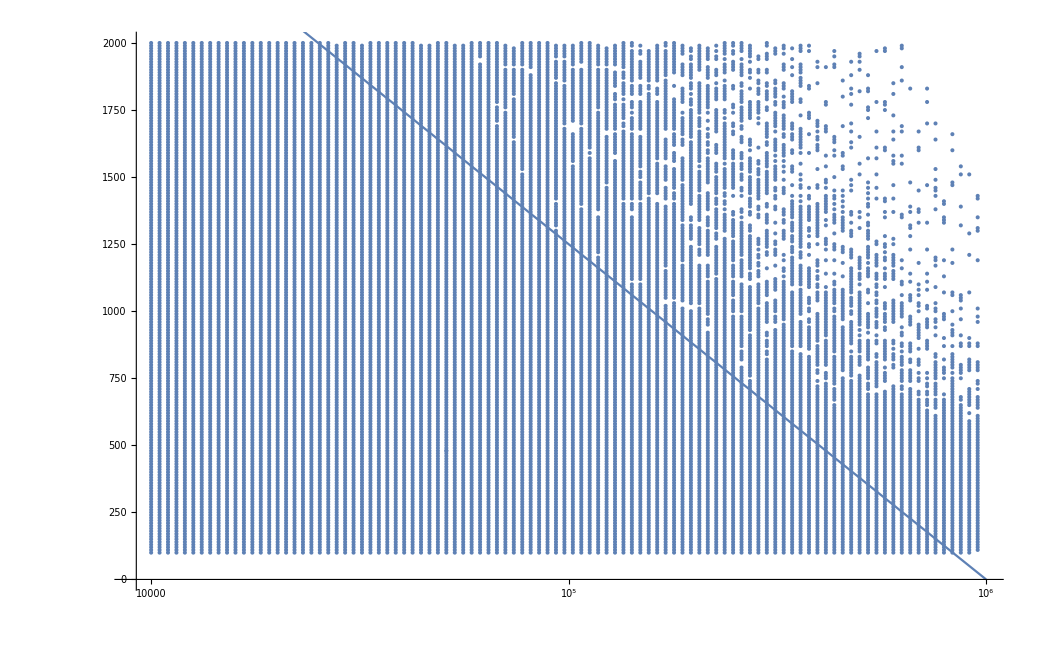

```mathematica
Show[ListLogLinearPlot[nHTsims,PlotRange->{{9000,1000000},All}],
LogLinearPlot[-2500/(Log[1000000]-Log[10000])(Log[x]-Log[10000])+2500,{x,10000,1000000}]]
```

```mathematica
nHgridpts//Dimensions
```

{100}

```mathematica
newnHTcorners=Select[Flatten[Outer[List,nHgridpts,Tgridpts],1],#[[2]]<-2500/(Log[1000000]-Log[10000])(Log[#[[1]]]-Log[10000])+2500&];
```

```mathematica
Complement[Round[newnHTcorners],Round[nHTsims]]
```

{{29151,100},{29151,110},{29151,120},{29151,130},{29151,140},{29151,150},{29151,160},{29151,170},{29151,180},{29151,190},{29151,200},{29151,210},{29151,220},{29151,230},{29151,240},{29151,250},{29151,260},{29151,270},{29151,280},{29151,290},{29151,300},{29151,310},{29151,320},{29151,330},{29151,340},{29151,350},{29151,360},{29151,370},{29151,380},{29151,390},{29151,400},{29151,410},{29151,420},{29151,430},{29151,440},{29151,450},{29151,460},{29151,470},{29151,480},{29151,490},{29151,500},{29151,510},{29151,520},{29151,530},{29151,540},{29151,550},{29151,560},{29151,570},{29151,580},{29151,590},{29151,600},{29151,610},{29151,620},{29151,630},{29151,640},{29151,650},{29151,660},{29151,670},{29151,680},{29151,690},{29151,700},{29151,710},{29151,720},{29151,730},{29151,740},{29151,750},{29151,760},{29151,770},{29151,780},{29151,790},{29151,800},{29151,810},{29151,820},{29151,830},{29151,840},{29151,850},{29151,860},{29151,870},{29151,880},{29151,890},{29151,900},{29151,910},{29151,920},{29151,930},{29151,940},{29151,950},{29151,960},{29151,970},{29151,980},{29151,990},{29151,1000},{29151,1010},{29151,1020},{29151,1030},{29151,1040},{29151,1050},{29151,1060},{29151,1070},{29151,1080},{29151,1090},{29151,1100},{29151,1110},{29151,1120},{29151,1130},{29151,1140},{29151,1150},{29151,1160},{29151,1170},{29151,1180},{29151,1190},{29151,1200},{29151,1210},{29151,1220},{29151,1230},{29151,1240},{29151,1250},{29151,1260},{29151,1270},{29151,1280},{29151,1290},{29151,1300},{29151,1310},{29151,1320},{29151,1330},{29151,1340},{29151,1350},{29151,1360},{29151,1370},{29151,1380},{29151,1390},{29151,1400},{29151,1410},{29151,1420},{29151,1430},{29151,1440},{29151,1450},{29151,1460},{29151,1470},{29151,1480},{29151,1490},{29151,1500},{29151,1510},{29151,1520},{29151,1530},{29151,1540},{29151,1550},{29151,1560},{29151,1570},{29151,1580},{29151,1590},{29151,1600},{29151,1610},{29151,1620},{29151,1630},{29151,1640},{29151,1650},{29151,1660},{29151,1670},{29151,1680},{29151,1690},{29151,1700},{29151,1710},{29151,1720},{29151,1730},{29151,1740},{29151,1750},{29151,1760},{29151,1770},{29151,1780},{29151,1790},{29151,1800},{29151,1810},{29151,1820},{29151,1830},{29151,1840},{29151,1850},{29151,1860},{29151,1870},{29151,1880},{29151,1890},{29151,1900},{29151,1910}}

```mathematica
newnHTpairs=Select[Flatten[Outer[List,MovingAverage[#,2]&@nHgridpts,MovingAverage[#,2]&@Tgridpts],1],#[[2]]<-2500/(Log[1000000]-Log[10000])(Log[#[[1]]]-Log[10000])+2500&];
```

```mathematica
belowcurvestrings="sleep 2; cd /lustre/janus_scratch/chaffin/3d_thomas_model/; ./simulate_coronal_scan.x -n "<>ToString[#[[1]]]<>" -T "<>ToString[#[[2]]]<>" fake_corona_obs_small.dat"&/@newnHTpairs;
```

```mathematica
belowcurvesimfiletext=StringJoin[Riffle[RandomSample[belowcurvestrings],"\n"]];
```

```mathematica
Export["below_curve_populate_parameter_space_commands",belowcurvesimfiletext,"Text"]
```

below_curve_populate_parameter_space_commands